## Log

07/27/2016 TM-- Updated the following features
			File format for saving all parameters was changed to mathematica file from excel file.
			Reading in Parameters section was added.
			PairConnect3 was added. This function connects the nearest spot instead of the first encountered near enough spot.
				Slower than PairConnect2, about a double the speed, but there should not be error.
			PairConnect4 was added. This fucntion gets rid of diversion of tracks.
			LinkTrack2 was added. This function gets rid of tracks which last shorter than threshold. And asign new track numbers.
				This avoids very big track numbers.

07/23/2016 TS -- Updated to match ParticleTracking_for_puro_2Colors.nb, which is what TM used in the Science translation paper. 

9/25/2015 TS -- Updated 3-color Find Red/Green/Blue Particles so that it shows the first “10” (endtest-starttest) and last “10” frames of movies to see if the threshhold works well for the entire movie. 

10/01/18 CC -- merged myROI with particle track code so I can shift mask throughout the movie---it works!!! holy shittt

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"];
```

## Functions and PSF

### MyROI[{img, img, ...},outfile]

```mathematica
MyROI[allimage:{_?ImageQ..},outfile_?StringQ]:=Module[{allimg=allimage},
DynamicModule[{Nimg=Length[allimg],thold,myt=1,y=1,myflag="  Ready.",Colors={Black,Red,Green,Blue,Purple,Orange,Brown,Gray,Pink,Cyan},w,h,mymask,mymaska,mymaskb,mynewmask,zoom,mymaskc,mytable,mytemptable,myCentroid,myroi,chN,mycurpoints,mysavepoints,mytemppoints,r={0,0},cury,numy,roin=30,roit,myshape,p1,p2,Size,Ns,roic,mydata,bd, tholdch,tholdsize,myflag2=" ",sizemean=1,mycc},
mynewmask=0;
thold=0.8;
tholdsize=9;
tholdch=1;
{w,h}=allimg⟦1⟧//ImageDimensions;
mytable=Table[0.,{i,1,h,1},{j,1,w,1}];
bd=allimg⟦1⟧//ImageType;
chN=allimg⟦1⟧//ImageChannels;
mysavepoints=Table[{{{1.,1.}},1.,If[chN>1,Table[1.,{i,1,chN,1}],1],1.},{i,1,30,1},{j,1,Nimg,1}];
mycurpoints=Table[{{{1.,1.}},1.,If[chN>1,Table[1.,{i,1,chN,1}],1],1.},{i,1,30,1}];

(*CHECK FOR PREVIOUS ROI FILES*)
If[FileNames[outfile]≠{},
mytemppoints=(<<(outfile));
Ns=Length[mytemppoints⟦1⟧];
If[Ns≤Nimg,
mysavepoints⟦1;;All,1;;Ns⟧=mytemppoints⟦1;;All,1;;Ns⟧;,mysavepoints⟦1;;All,1;;Nimg⟧=mytemppoints⟦1;;All,1;;Nimg⟧;
];
Clear[mytemppoints];
];

(*CONTROLS............................*)
Column[{
Row[{"ROI:" PopupMenu[Dynamic[y],Join[{1->"Background",2->"Cytoplasm",3->"Nucleus",4->"Nucleoli",5->"Array",6->"ROI6"},Table[i->"ROI"<>ToString[i],{i,7,roin,1}]]],
"  Type:" PopupMenu[Dynamic[roit],{1->"Polygon",2->"Rectangle",3->"Circle"}],Spacer[10],
Button["EXPORT ROI CALC FILE",
If[FileNames[outfile]=={},
mysavepoints>>(outfile); myflag=outfile<>"  File saved.",myflag="   ROIs file already exists."
]],
Button["DELETE ROI CALC FILE",
If[FileNames[outfile]≠{},
DeleteFile[outfile];myflag="  File deleted.",myflag="   No ROIs file found.";
]],
Button["CALCULATE AUTO ROI",
mymaska=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mynewmask=mymaska;
mymaskb=Binarize[ImageMultiply[mymaska,ColorSeparate[allimg⟦myt⟧]⟦tholdch⟧//ImageAdjust],thold];
myCentroid=Round[#,1]&/@(Position[mymaskb//ImageData,1]//Mean);
roit=3;
mymaskc=Binarize@Image[Graphics[{White,Disk[{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},tholdsize]},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mymask=ImageSubtract[mymaskc,mymaskb];
mycurpoints⟦y,1⟧={{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1}+{tholdsize,0}};
mycurpoints⟦y,2⟧=Count[mymaskc//ImageData//Chop//Flatten,x_/;x≠ 0.]//N;
mysavepoints⟦y,myt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,myt,3⟧=Plus@@(ImageData[ImageMultiply[mymaskc,allimg⟦myt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,myt,4⟧=3;
],
" Threshhold: ",InputField[Dynamic[thold],FieldSize->3],"  Channel:" PopupMenu[Dynamic[tholdch],{1->"1, red",2->"2, green",3->"3, blue"}],"  ROI Size: ",InputField[Dynamic[tholdsize],FieldSize->3],
Button["CACULATE AUTO ROI FORWARD",
mymaska=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
Table[
mymaskb=Binarize[ImageMultiply[mymaska,ColorSeparate[allimg⟦tt⟧]⟦tholdch⟧//ImageAdjust],thold];
myCentroid=Round[#,1]&/@(Position[mymaskb//ImageData,1]//Mean);
roit=3;
mymaskc=Binarize@Image[Graphics[{White,Disk[{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},tholdsize]},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mymask=ImageSubtract[mymaskc,mymaskb];
mycurpoints⟦y,1⟧={{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1}+{tholdsize,0}};
mycurpoints⟦y,2⟧=Count[mymaskc//ImageData//Chop//Flatten,x_/;x≠ 0.]//N;
mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymaskc,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,Nimg,1}];
],
Dynamic[myflag],Dynamic[myflag2],
}],
Row[{
Button["CALCULATE ROI BACK",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
Table[mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,1,-1}];
],
Button["CALCULATE ROI",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
mysavepoints⟦y,myt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,myt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦myt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,myt,4⟧=roit;
],
Button["CALCULATE ROI FORWARD",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
Table[mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,Nimg,1}];
],
Button["CLEAR ROI",Dynamic[mycurpoints⟦y⟧={{{1,1}},1,0}]],
Button["SHOW ROI",
If[FileNames[outfile]≠{},
mytemppoints=(<<(outfile));
Ns=Length[mytemppoints⟦1⟧];
If[myt≤Ns,
mycurpoints⟦y⟧=mytemppoints⟦y,myt⟧;
roit=mysavepoints⟦y,myt,4⟧;
myflag="  Imported ROI.",
myflag="  No ROI saved.";
];,myflag="  No ROI file found."
]
],
Spacer[10],
{Button["<",mycurpoints⟦y,1⟧=(#-{1,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center],
Column[
{
Button["^",mycurpoints⟦y,1⟧=(#+{0,1})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}],
Button["⋁",mycurpoints⟦y,1⟧=(#-{0,1})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}]
},
BaselinePosition->Center],
Button[">",mycurpoints⟦y,1⟧=(#+{1,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center]}//Row[#,BaselinePosition->Bottom]&,
Spacer[10],
{Button["⇐",mycurpoints⟦y,1⟧=(#-{30,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center],
Column[
{
Button["⇑",mycurpoints⟦y,1⟧=(#+{0,30})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}],
Button["⇓",mycurpoints⟦y,1⟧=(#-{0,30})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}]
},
BaselinePosition->Center],
Button["⇒",mycurpoints⟦y,1⟧=(#+{30,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center]}//Row[#,BaselinePosition->Bottom]&
}],

(*Dynamically updated content........................*)
Row[{Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]}],
Row[{Slider[Dynamic[zoom],{300,1500,10},ImageSize->{600,20}] }],
Row[{"Choose Channel: "PopupMenu[Dynamic[mycc],Table[i->"Channel "<>ToString[i],{i,0,chN,1}]]}],
Row[{

Manipulate[LocatorPane[Dynamic[mycurpoints⟦y,1⟧],
Show[If[mycc>0,ImageAdjust[ColorSeparate[allimg⟦myt⟧]⟦mycc⟧],
ImageAdjust[allimg⟦myt⟧]],ImageSize->{zoom}],LocatorAutoCreate->True,Appearance->"+"],{{br,30},0.1,100,0.01},ControlType->{VerticalSlider},ControlPlacement->Left],
Spacer[10],Dynamic[
GraphicsColumn[
(#//ImageAdjust//Show[{#,Graphics[{EdgeForm[Directive[Yellow]],Opacity[0.],
myshape=If[roit==1,Polygon[mycurpoints⟦y,1⟧],
If[roit==2,
p1={Min[mycurpoints⟦y,1,1;;All,1⟧],Min[mycurpoints⟦y,1,1;;All,2⟧]};
p2={Max[mycurpoints⟦y,1,1;;All,1⟧],Max[mycurpoints⟦y,1,1;;All,2⟧]};
myflag="  dim="<>ToString[Round[Abs[p1-p2],1]];
Rectangle[p1,p2],
If[roit==3,
p1={Max[mycurpoints⟦y,1,1;;All,1⟧],Max[mycurpoints⟦y,1,1;;All,2⟧]};p2={Min[mycurpoints⟦y,1,1;;All,1⟧],Min[mycurpoints⟦y,1,1;;All,2⟧]};
Size=√((p1-p2).(p1-p2));
myflag="  radius="<>ToString[Round[Size,1]];
Disk[mycurpoints⟦y,1,1⟧,Size]]]]}]}]&)&/@ColorSeparate[allimg⟦myt⟧],
Background->{Red,Green,Blue,Orange,Purple,Pink,Black,Gray,Brown},ImageSize->{500}]],
Dynamic[
mydata=If[sizemean==1,If[chN==1,mysavepoints⟦y,1;;All,3⟧/If[cury==0,1,mysavepoints⟦cury,1;;All,3⟧],mysavepoints⟦y,1;;All,3⟧/If[cury==0,1,mysavepoints⟦cury,1;;All,3⟧]//Transpose],mysavepoints⟦y,1;;All,2⟧];
Column[{
Row[{Spacer[130],
"ROI /"PopupMenu[Dynamic[cury],Join[{0->"Choose Divider",1->"Background",2->"Cytoplasm",3->"Nucleus",4->"Nucleoli",5->"Array",6->"ROI6"},Table[i->"ROI"<>ToString[i],{i,7,30,1}]]]
}],
Row[{Spacer[130],
"Measure:"PopupMenu[Dynamic[sizemean],{0->"ROI Size",1->"ROI Mean Int."}]
}],
ListPlot[mydata,Joined->True,Frame->True,FrameTicks->{{All,All},{All,All}},FrameLabel->{"Image #", If[sizemean==1,"Mean Int.","ROI Size (pixels)"]},PlotMarkers->{Automatic,8} ,PlotStyle->Colors⟦2;;All⟧,AxesOrigin->{0,Automatic},ImageSize->300,AspectRatio->1,PlotRange->{{0,Nimg+1},All}]//Show[{#,Graphics[{Purple,Dashed,Line[{{myt,-1000},{myt,1000}}]}]}]&

},Dynamic[mymask]]]
}]
}]//Panel
]]
```

### MyNumString

```mathematica
MyNumString[myn_,L_]:=If[myn>10^L-1,IntegerString[myn,10,L+1],IntegerString[myn,10,L]];
```

```mathematica
MyNumString[30,3]
```

030

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### FindParticles (updated to remove adjacentbordercounts)

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,7]&; 
t2=track2//Flatten//Partition[#,7]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
ol={t1⟦All,{2,1,3,4,5,6,7}⟧,t2⟦All,{2,1,3,4,5,6,7}⟧}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_optional]

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color,FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

### TickFormat[xmin_,xmax_,digits_,divisions_]

```mathematica
TickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

### MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_optional]

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{Table[mybinsize i,{i,1,60,1}]},"Probability",PlotTheme->"Detailed",FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{bins},"Probability",PlotTheme->"Detailed",Frame->True,FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

### TXYDiffusionPlotter[txylsits,maxt,color,shapeN,size]

```mathematica
TXYDiffusionPlotter[txylists_,maxt_,color_,shapeN_,size_]:=Module[{msds,p1,p2,msds2},
msds=Table[{#⟦1⟧,(#⟦2⟧+#⟦3⟧)^2}&/@Differences[txylists⟦i⟧,1,j],{i,1,Length[txylists],1},{j,1,maxt,1}];
p1=Table[Mean/@msds[[i]],{i,1,Length[msds],1}]//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
msds2=msds//Flatten//Partition[#,2]&//Union//SplitBy[#,First]&;
p2={(Mean/@msds2),ErrorBar/@(StandardDeviation[#]/(√Length[#])&/@msds2⟦All,All,2⟧)}//Transpose//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxt-1},All},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}
,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color]&;
{p1,p2}
]
```

### InteractionAnalyzer[componentAnalysisList_,column_(3=red,4=green,5=blue),shapeN,size]

```mathematica
InteractionAnalyzer[ca_,column_,shapeN_,size_]:=Module[{goodi,redis,p1,greenis,p2,blueis,p3,myAvgBlueis,myAvgRedis,myAvgGreenis,mySizes,p4,p5,p6,p4d,p5d,p6d,p7},
(*We need to delete those cases when we cannot see, eg., blue in every track (assuming blue is the seed column for the track). In other words, sometimes we cannot match up the centroid to a specific track. In that case, we will not include in the analysis. *)
goodi=1+Position[Table[Count[MovingAverage[ca[[i,All,column]],2],x_/;NumericQ[x]==True&&x≠0]/(Length[ca⟦i⟧]-1),{i,2,Length[ca],1}],1]//Flatten;
redis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,3]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p1=redis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Red to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
greenis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,4]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p2=greenis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Green to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
blueis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,5]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p3=blueis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Blue to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
myAvgRedis=Mean/@redis;
myAvgGreenis=Mean/@greenis;
myAvgBlueis=Mean/@blueis;
mySizes=N[Mean/@ca⟦goodi,1;;All,If[column==5,8,If[column==4,7,6]]⟧];
p4d={myAvgRedis,mySizes}//Transpose;
p4=p4d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Red Int'n Time",FrameLabel->{"Avg. red int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p5d={myAvgGreenis,mySizes}//Transpose;
p5=p5d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Green Int'n Time",FrameLabel->{"Avg. green int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p6d={myAvgBlueis,mySizes}//Transpose;
p6=p6d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Blue Int'n Time",FrameLabel->{"Avg. blue int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p7=(MovingAverage[#,3]&/@ca[[goodi,All,If[column==5,8,If[column==4,7,6]]]])//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotLabel->"Size of Tracked "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Clusters",FrameLabel->{"Time (frames)","Size (pixels)"},PlotRange->All,PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}]&;
If[column==5,p6=p7,If[column==4,p5=p7,p4=p7]];
{redis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,greenis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,blueis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,p4d,p5d,p6d,p1,p2,p3,p4,p5,p6}
]
```

### MyMSDPlotter[myColorParameter_,color_]

```mathematica
MyMSDPlotter[myColorParameter_,color_]:=Module[{msds,p1,p2,poz},
mycol=If[color=="Red"||color=="Darker[Yellow,0.2]"||color=="Purple"||color=="White",13,If[color=="Green"||color=="Cyan",15,17]];
If[myColorParameter≠{},
msds=Table[poz=myColorParameter[[j,1;;All,mycol;;mycol+1]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[myColorParameter],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2=Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->ToExpression[color]]&;
{p2,p1}
]
]
```

### My3DImager[dir_, fileNameHead_, myt_, myx_, myy_, myc_, dimxy_, dz_, rangez_] dz in nanometers, assuming pixels are 130 nm

```mathematica
My3DImager[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&;
myGrid=Grid[{{myImg3D//Image3DProjection[#,"YZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageRotate[#,-π/2]&,myImg3D//Image3DProjection[#,"XY"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),1.3 (2 dimxy +1) }]&},{, myImg3D//Image3DProjection[#,"XZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageReflect[#,Left->Right]&}}]
]
```

```mathematica
My3DImagerRaw[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&
]
```

### MyAutoCorrelate[list]

```mathematica
ml={a,b,c,d,e};ListCorrelate[ml,ml,{1,1},0]
```

{a^2+b^2+c^2+d^2+e^2,a b+b c+c d+d e,a c+b d+c e,a d+b e,a e}

```mathematica
MyAutoCorrelate[list_]:=Module[{},
1/(Mean[list])^2 ListCorrelate[list-Mean[list],list-Mean[list],{1,1},0] Reverse[1/Range[Length[list]]]
]
```

```mathematica
MyAutoCorrelate[ml];
```

## Analysis

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymoviefile]],Dynamic[mymoviefile]}
```

{$CellContext`mymoviefileOpenAll,}

```mathematica
mymoviefile=If[StringTake[FileBaseName[mymoviefile],4]=="AVG_",StringReplace[mymoviefile,"AVG_"->""],mymoviefile];
```

```mathematica
(*
myColMovie=Import[mymoviefile]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymoviefile]<>"Analysis/"<>StringDrop[StringDelete[mymoviefile,DirectoryName[mymoviefile]],-4]; 
Use this for a mac ;) *)
```

```mathematica
myColMovie=Import[mymoviefile]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymoviefile]<>"Analysis/"<>StringDrop[StringDelete[mymoviefile,DirectoryName[mymoviefile]],-4];
```

```mathematica
myColMovie
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Determine ROI

```mathematica
mymovie = Import[mymoviefile];
```

```mathematica
ch1=ImageSubtract[#,500/2^16]&/@mymovie[[1;;All;;3]];
ch2=ImageSubtract[#,500/2^16]&/@mymovie[[2;;All;;3]];
ch3=ImageSubtract[#,500/2^16]&/@mymovie[[3;;All;;3]];
myColCombMov=Table[ColorCombine[{ch1[[i]],ch2[[i]],ch3[[i]]}],{i,1,Length[ch1],1}];
```

***If you have trouble with the myROI, a possible solution is that you already have a data file with the same name... 
***Try deleting the file manually in file explorer and shift+enter the myROI code again

```mathematica
MyROI[myColCombMov,analysisFolder<>"_myROI.dat"]
```

### Make Masks from myROI

***Import mask file:

```mathematica
mymaskfile = <<(analysisFolder<>"_myROI.dat");
```

```mathematica
mymaskfile[[2,All,3]]//Transpose
```

{{391.602,400.472},{4029.28,3266.},{1237.05,3223.1}}

```mathematica
{1237.0490889425078,3223.1024527494037}/{4029.2784341459355,3265.995718392562}
```

{0.307015,0.986867}

```mathematica
bkgGInt = mymaskfile[[1,All,3,2]]
cytoGInt = mymaskfile[[2,All,3,2]]
nucGInt = mymaskfile[[3,All,3,2]]
```

{910.007,1038.44}

{4029.28,3266.}

{4445.73,6162.37}

```mathematica
myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

{1.13351,2.30025}

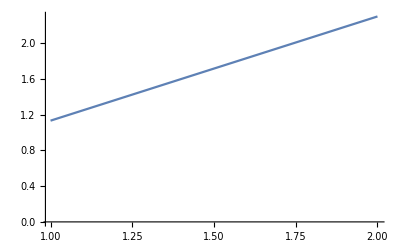

```mathematica
ListLinePlot[myRatio, PlotRange->All]
```

***Specify bkgrd and length of movie:

```mathematica
lenMov = mymaskfile[[1,All,1,All]]//Length;
mybkgdcoords = mymaskfile[[1,All,1,All]];
myCytoCoords = mymaskfile[[2,All,1,All]];
myNucCoords = mymaskfile[[3,All,1,All]];
dummyMov=Table[Image[Table[0,512^2,1]//Partition[#,512]&],{j,1,lenMov,1}];
```

***Find bkg, cyto, and nuc intensities:

```mathematica
bkgintensity = 
cytomask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[myCytoCoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
nucmask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[myNucCoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
```

***Make masks for cyto and nuc and bkgrd:

```mathematica
bkgmask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[mybkgdcoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
cytomask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[myCytoCoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
nucmask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[myNucCoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
```

```mathematica
cytomask//Dimensions
```

{2}

***Export as data files:

```mathematica
bkgmask>>(analysisFolder<>"_myBkgMask.dat")
cytomask>>(analysisFolder<>"_myCytMask.dat")
(*
nucmask>>(analysisFolder<>"_myNucMask.dat")
*)
```

***Adding these variable calls so that the analysis stuff at the end of the code work... you DONT need these to do particle tracking:

```mathematica
mymask=-Graphics-;
myNucMask = nucmask[[1]];
```

### Creating Transformation Function

```mathematica
DirectoryName[mymoviefile]
```

C:\Users\Charlotte\Desktop\121917\121917TA\

```mathematica
"C:\\Users\\Charlotte\\Desktop\\121917\\121917TL\\"
```

```mathematica
dirBeads=DirectoryName[mymoviefile]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

Part::partd: Part specification myBeadsImgs⟦4,1⟧ is longer than depth of object.

Part::partd: Part specification myBeadsImgs⟦4,2⟧ is longer than depth of object.

ConstantImage::bddim: The specified dimensions myDims should be a positive integer or a list of positive integers for every spatial dimensions.

ColorCombine::ccbinput: {myBeadsImgs⟦4,1⟧,myBeadsImgs⟦4,2⟧,ConstantImage[0,myDims]} should be a list of images with the same image dimensions.

ImageAdjust::imginv: Expecting an image or graphics instead of ColorCombine[{myBeadsImgs⟦4,1⟧,myBeadsImgs⟦4,2⟧,ConstantImage[0,myDims]}].

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

21 red particles and 24 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

{0.0818794,TransformationFunction[(0.999136 | -0.00795461 | 5.64984
0.0050785 | 0.999355 | -4.08232
-7.02985×10^-7 | -4.76277×10^-6 | 1.)],Distance Before Correction | Distance After Correction
2.78392 | 0.110412
2.97465 | 0.1706
3.59869 | 0.059571
3.30613 | 0.0866425
3.43785 | 0.056925
3.68431 | 0.0426033
4.17258 | 0.110475
4.8759 | 0.00779529
4.70945 | 0.0719881
4.55286 | 0.101782}

```mathematica
Export[DirectoryName[mymoviefile]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

12 red particles and 11 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

Distance Before Correction | Distance After Correction
3.52268 | 0.237036
3.70134 | 0.24712
4.08483 | 0.257613
3.68448 | 0.334984
4.65206 | 0.0545464
4.57443 | 0.204799
4.32711 | 0.0882253
4.46865 | 0.123524

### Reading in Parameters (only if parameters exist)

```mathematica
myTfFunc=Import[DirectoryName[mymoviefile]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
analysisFolder
```

/Volumes/GRAD SCHOOL/20181025_27_TA_TL_NT_15h/Analysis/MAX_NT01

```mathematica
bkgmask=<<(analysisFolder<>"_myBkgMask.dat"); 
cytomask=<<(analysisFolder<>"_myCytMask.dat");
nucmask=<<(analysisFolder<>"_myNucMask.dat");
```

```mathematica
myParameters=<<(analysisFolder<>"_allParameters.dat");
{avgFrameN,thred,thred2,bandpassred,dotsizered,maxJumpDistRed,shortestTrackRed,thgreen,thgreen2,bandpassgreen,dotsizegreen,maxJumpDistGreen,shortestTrackGreen,thblue,thblue2,bandpassblue,dotsizeblue,maxJumpDistBlue,shortestTrackBlue,pad}=myParameters⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧;
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_allParameters.dat.

Part::partd: Part specification $Failed⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧ is longer than depth of object.

Set::shape: Lists {avgFrameN,thred,thred2,bandpassred,dotsizered,maxJumpDistRed,shortestTrackRed,thgreen,thgreen2,bandpassgreen,dotsizegreen,maxJumpDistGreen,shortestTrackGreen,thblue,thblue2,bandpassblue,dotsizeblue,maxJumpDistBlue,shortestTrackBlue,pad} and $Failed⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧ are not the same shape.

```mathematica
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
redRunAvp=<<(analysisFolder<>"_redspots.dat");
greenRunAvp=<<(analysisFolder<>"_greenspots.dat");
blueRunAvp=<<(analysisFolder<>"_bluespots.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenspots.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_bluespots.dat.

```mathematica
myredtracks=<<(analysisFolder<>"_redtracks.dat");
mygreentracks=<<(analysisFolder<>"_greentracks.dat");
mybluetracks=<<(analysisFolder<>"_bluetracks.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_redtracks.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greentracks.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_bluetracks.dat.

```mathematica
newTracksr=<<(analysisFolder<>"_RedTracksColorLinked.dat");
newTracksg=<<(analysisFolder<>"_GreenTracksColorLinked.dat");
newTracksb=<<(analysisFolder<>"_BlueTracksColorLinked.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_RedTracksColorLinked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_GreenTracksColorLinked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_BlueTracksColorLinked.dat.

```mathematica
myHandCheckedTracksr=<<(analysisFolder<>"_RedTracksHandChecked.dat");
myHandCheckedTracksg=<<(analysisFolder<>"_GreenTracksHandChecked.dat");
myHandCheckedTracksb=<<(analysisFolder<>"_BlueTracksHandChecked.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_RedTracksHandChecked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_GreenTracksHandChecked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_BlueTracksHandChecked.dat.

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=<<(analysisFolder<>"_bluefits.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_bluefits.dat.

Set::shape: Lists {myBlueAllParameters,myBluePos,myBlueData} and $Failed are not the same shape.

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_redfits.dat.

Set::shape: Lists {myRedAllParameters,myRedPos,myRedData} and $Failed are not the same shape.

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=<<(analysisFolder<>"_greenfits.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenfits.dat.

Set::shape: Lists {myGreenAllParameters,myGreenPos,myGreenData} and $Failed are not the same shape.

```mathematica
myTfFunc=Import[DirectoryName[mymoviefile]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
mylongredtracksf=mylongredtracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

0 red tracks are longer than shortestTrackRed, and the average length of the long tracks is Mean[$Failed]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylonggreentracks//Length,shortestTrackGreen,(Length/@mylonggreentracks)//Mean//N]
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

0 green tracks are longer than shortestTrackGreen, and the average length of the long tracks is Mean[$Failed]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylongbluetracks//Length,shortestTrackBlue,(Length/@mylongbluetracks)//Mean//N]
mylongbluetracksf=mylongbluetracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

0 green tracks are longer than shortestTrackBlue, and the average length of the long tracks is Mean[$Failed]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
mymask=<<(analysisFolder<>"_mymask.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_mymask.dat.

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_myNucMask.dat.

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
analysisFolder
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28

```mathematica
(*mymask=Import[analysisFolder<>"_nucleus_mask.tif"];*)
```

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_myNucMask.dat.

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
myCytImg=myCytMask;
```

```mathematica
myNucImg=myNucMask;
```

```mathematica
redComponentMask=Import[analysisFolder<>"_redComponentMask.tif"];
```

```mathematica
analysisFolder<>"_greenComponentMask.tif"
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenComponentMask.tif

```mathematica
greenComponentMask=Import[analysisFolder<>"_greenComponentMask.tif"];
```

Import::nffil: File not found during Import.

```mathematica
blueComponentMask=Import[analysisFolder<>"_blueComponentMask.tif"];
```

Import::nffil: File not found during Import.

```mathematica
whitePlot=<<(analysisFolder<>"_whitePlot.dat");
purplePlot=<<(analysisFolder<>"_purplePlot.dat");
yellowPlot=<<(analysisFolder<>"_yellowPlot.dat");
cyanPlot=<<(analysisFolder<>"_cyanPlot.dat");
redPlot=<<(analysisFolder<>"_redPlot.dat");
greenPlot=<<(analysisFolder<>"_greenOnlyPlot.dat");
bluePlot=<<(analysisFolder<>"_blueOnlyPlot.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_whitePlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_purplePlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_yellowPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_cyanPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_redPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenOnlyPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_blueOnlyPlot.dat.

```mathematica
myWhiteColorParameters=<<(analysisFolder<>"_FixedSigmaWhiteColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaWhiteColorParameters.dat.

```mathematica
myYellowColorParameters=<<(analysisFolder<>"_FixedSigmaYellowColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaYellowColorParameters.dat.

```mathematica
myPurpleColorParameters=<<(analysisFolder<>"_FixedSigmaPurpleColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaPurpleColorParameters.dat.

```mathematica
myCyanColorParameters=<<(analysisFolder<>"_FixedSigmaCyanColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaCyanColorParameters.dat.

```mathematica
myRedOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaRedOnlyColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaRedOnlyColorParameters.dat.

```mathematica
myGreenOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaGreenOnlyColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaGreenOnlyColorParameters.dat.

```mathematica
myBlueOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaBlueOnlyColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaBlueOnlyColorParameters.dat.

```mathematica
minOverlapTime=5; (*in frames*)
maxOverlapDistance=3;(*in pixels*)
```

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

### Running z-average

```mathematica
avgFrameN=1;
myMaxN=Length[myColMovie[[1,All]]]-avgFrameN+1
```

24

```mathematica
(*
myCytoMovieRunAv = Transpose[Partition[cytomaskmov,3]];
*)
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
Dimensions/@myColMovie
```

{{24},{24},{24}}

```mathematica
(*
myCytoMovieRunAv=Table[ImageMultiply[ImageAdd[temp⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
*)
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,1,Length[myColMovieRunAv],1},{frame,1,myMaxN,1},{threshold,0,0.2,0.001}]
```

### Find Red Particles from Running z - averaged Movie (Red laser)

```mathematica
(* redRunAvp is list of {{x1,y1},{x2,y2}....{xn,yn}} in each frame *)
```

```mathematica
Manipulate[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thred={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦1⟧],1},{{threshold1,0.001},0,0.6,0.001},{{threshold2,0.03},0,0.6,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦1, 1⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,cytomask[[1]]],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦1, frame⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦1,frame⟧// ImageAdjust[#, {0, 0, 1}, thred]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],cytomask[[frame]]],"Count",lo<#<hi&]},ImageSize->900],
Button["Choose parameters and CLICK",{mymaxred=max,bandpassred={lowpass,hipass},thred2=threshold,dotsizered={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,30,1},{{lo,5},0,20,1},{{hi,100},50,500,1}]
```

```mathematica
redRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,cytomask[[frame]],dotsizered],{frame,1,myMaxN,1}];
StringForm["   `` red particles were found.",redRunAvp//Flatten[#,1]&//Length]
```

840 red particles were found.

```mathematica
redComponentMask=Table[ImageTransformation[FindParticlesWeightedMask[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,cytomask[[frame]],dotsizered],myTfFuncInv,DataRange->Full],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,
Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",redRunAvp>>analysisFolder<>"_redspots.dat";Export[analysisFolder<>"_redComponentMask.tif",redComponentMask];],{frame,1,myMaxN,1}]
```

```mathematica
redRunAvp>>analysisFolder<>"_redspots.dat";
```

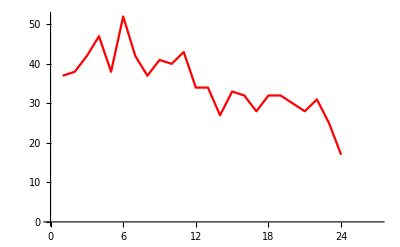

```mathematica
rSpotNPlot=Length/@redRunAvp//ListLinePlot[#,PlotStyle->Red, PlotRange->{{0,27},{0,All}}]&
```

### Find Green Particles from Running z-averaged Movie (Green laser)

```mathematica
Manipulate[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thgreen={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦2⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,1,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦2, 1⟧ // ImageAdjust[#, {0, 0, 1}, thgreen] &,cytomask[[1]]],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦2, frame⟧ // ImageAdjust[#, {0, 0, 1}, thgreen] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦2,frame⟧// ImageAdjust[#, {0, 0, 1}, thgreen]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],cytomask[[frame]]],"Count",lo<#<hi&]},ImageSize->900],
Button["Choose parameters and CLICK",{mymaxgreen=max,bandpassgreen={lowpass,hipass},thgreen2=threshold,dotsizegreen={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,30,1},{{lo,5},0,20,1},{{hi,100},10,500,1}]
```

```mathematica
greenRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,cytomask[[frame]],dotsizegreen],{frame,1,myMaxN,1}];
StringForm["`` green particles were found.",greenRunAvp//Flatten[#,1]&//Length]
```

605 green particles were found.

```mathematica
greenComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,cytomask[[frame]],dotsizegreen],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Green,Circle[#,5]&/@(greenRunAvp⟦frame⟧)}],Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",greenRunAvp>>analysisFolder<>"_greenspots.dat";Export[analysisFolder<>"_greenComponentMask.tif",greenComponentMask];],
{frame,1,myMaxN,1}]
```

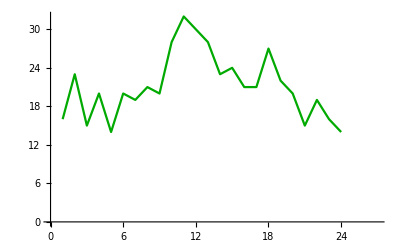

```mathematica
rSpotNPlot=Length/@greenRunAvp//ListLinePlot[#,PlotStyle->Darker[Green],PlotRange->{{0,27},{0,All}}]&
```

### Find Blue Particles from Running z-averaged Movie (Blue laser)

```mathematica
Manipulate[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thblue={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦3⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,0.4,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦3, 1⟧ // ImageAdjust[#, {0, 0, 1}, thblue] &,cytomask[[1]]],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦3, frame⟧ // ImageAdjust[#, {0, 0, 1}, thblue] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦3,frame⟧// ImageAdjust[#, {0, 0, 1}, thblue]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],cytomask[[frame]]],"Count",lo<#<hi&]},ImageSize->900],
Button["Choose parameters and CLICK",{mymaxblue=max,bandpassblue={lowpass,hipass},thblue2=threshold,dotsizeblue={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,6},0,10,1},{{lo,3},0,20,1},{{hi,200},50,500,1}]
```

```mathematica
blueRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,cytomask[[frame]],
dotsizeblue],{frame,1,myMaxN,1}];
StringForm["`` blue particles were found.",blueRunAvp//Flatten[#,1]&//Length]
```

340 blue particles were found.

```mathematica
blueComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,cytomask[[frame]],dotsizeblue],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}],Graphics[{Green,Circle[#,7]&/@(greenRunAvp⟦frame⟧)}],Graphics[{Blue,Circle[#,7]&/@(blueRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",blueRunAvp>>analysisFolder<>"_bluespots.dat";Export[analysisFolder<>"_blueComponentMask.tif",blueComponentMask];],
{frame,1,myMaxN,1}]
```

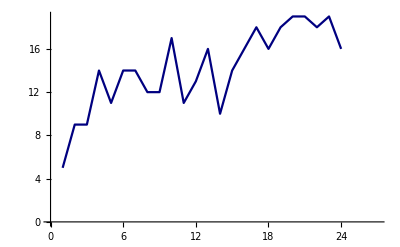

```mathematica
Length/@blueRunAvp//ListLinePlot[#,PlotStyle->Darker[Blue,0.5],PlotRange->{{0,27},{0,All}}]&
```

### Fitting Tracks with Gaussian

#### Setting Parameters

```mathematica
pad=7;
myTrimSize=2*pad+1;
```

#### Fitting red tracks with Gaussian

```mathematica
{myRedAllParameters,myRedPos,myRedData}=ParticleFittingFixedSigma[myColMovie,1,myHandCheckedTracksr,pad,myTrimSize,1.5,avgFrameN];
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}>>analysisFolder<>"_redfits.dat";
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

```mathematica
myRedAllParametersColReg=myRedAllParameters;
myRedAllParametersColReg⟦All,3;;4⟧=myTfFunc/@myRedAllParameters⟦All,3;;4⟧;
```

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
myRedAllParametersColRegLabeled=Insert[myRedAllParametersColReg,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaRedAllParameters.xls",myRedAllParametersColRegLabeled];
```

#### Fitting green tracks with Gaussian

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=ParticleFittingFixedSigma[myColMovie,2,myHandCheckedTracksg,pad,myTrimSize,1.5,avgFrameN];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}>>analysisFolder<>"_greenfits.dat";
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=<<(analysisFolder<>"_greenfits.dat");
```

```mathematica
myGreenAllParametersLabeled=Insert[myGreenAllParameters,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaGreenAllParameters.xls",myGreenAllParametersLabeled];
```

#### Fitting blue tracks with Gaussian

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=ParticleFittingFixedSigma[myColMovie,3,myHandCheckedTracksb,pad,myTrimSize,1.5,avgFrameN];
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}>>analysisFolder<>"_bluefits.dat";
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=<<(analysisFolder<>"_bluefits.dat");
```

```mathematica
myBlueAllParametersLabeled=Insert[myBlueAllParameters,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaBlueAllParameters.xls",myBlueAllParametersLabeled];
```

### Saving parameters

```mathematica
mylabelParameters4xls={"Running Average Size","Lower Threshold Red #1","Higher Threshold Red #1","Threshold Red #2","Lower BandPass Red","Higher BandPass Red","Lower Excluded Particle Size Red","Higher Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Lower Threshold Green #1","Higher Threshold Green #1","Threshold Green #2","Lower BandPass Green","Higher BandPass Green","Lower Excluded Particle Size Green","Higher Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Lower Threshold Blue #1","Higher Threshold Blue #1","Threshold Blue #2","Lower BandPass Blue","Higher BandPass Blue","Lower Excluded Particle Size Blue","Higher Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"
};
myParameters={avgFrameN,thred⟦1⟧,thred⟦2⟧,thred2,bandpassred⟦1⟧,bandpassred⟦2⟧,dotsizered⟦1⟧,dotsizered⟦2⟧,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen⟦1⟧,thgreen⟦2⟧,thgreen2,bandpassgreen⟦1⟧,bandpassgreen⟦2⟧,dotsizegreen⟦1⟧,dotsizegreen⟦2⟧,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue⟦1⟧,thblue⟦2⟧,thblue2,bandpassblue⟦1⟧,bandpassblue⟦2⟧,dotsizeblue⟦1⟧,dotsizeblue⟦2⟧,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Export[analysisFolder<>"_allParameters.xls",Thread@{mylabelParameters4xls,myParameters}];
```

```mathematica
mylabelParameters={"Running Average Size","Threshold Red #1","Threshold Red #2","BandPass Red","Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Threshold Green #1","Threshold Green #2","BandPass Green","Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Threshold Blue #1","Threshold Blue #2","BandPass Blue","Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"};
myParameters={avgFrameN,thred,thred2,bandpassred,dotsizered,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen,thgreen2,bandpassgreen,dotsizegreen,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue,thblue2,bandpassblue,dotsizeblue,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Thread@{mylabelParameters,myParameters}>>analysisFolder<>"_allParameters.dat";
Export[DirectoryName[mymoviefile]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
mylabelParameters={"Running Average Size","Threshold Red #1","Threshold Red #2","BandPass Red","Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Threshold Green #1","Threshold Green #2","BandPass Green","Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Threshold Blue #1","Threshold Blue #2","BandPass Blue","Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"};
myParameters={avgFrameN,thred,thred2,bandpassred,dotsizered,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen,thgreen2,bandpassgreen,dotsizegreen,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue,thblue2,bandpassblue,dotsizeblue,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Thread@{mylabelParameters,myParameters}//TableForm
```

Running Average Size | 1
Threshold Red #1 | 0.001
0.05
Threshold Red #2 | 0.06
BandPass Red | 1
7
Excluded Particle Size Red | 5
40
Detected Red Particles | 840
Maximum Jump Distance for Red | maxJumpDistRed
Detected Red Tracks | 0
Average Length of Red Tracks | Mean[myredtracks]
Shortest Length for Red Long Tracks | shortestTrackRed
Detected Red Long Tracks | 0
Average Length of Red Long Tracks | Mean[mylongredtracks]
Threshold Green #1 | 0.015
0.194
Threshold Green #2 | 0.09
BandPass Green | 1
7
Excluded Particle Size Green | 5
45
Detected Green Particles | 605
Maximum Jump Distance for Green | maxJumpDistGreen
Detected Green Tracks | 0
Average Length of Green Tracks | Mean[mygreentracks]
Shortest Length for Green Long Tracks | shortestTrackGreen
Detected Green Long Tracks | 0
Average Length of Green Long Tracks | Mean[mylonggreentracks]
Threshold Blue #1 | 0.01
0.123
Threshold Blue #2 | 0.09
BandPass Blue | 1
6
Excluded Particle Size Blue | 3
200
Detected Blue Particles | 340
Maximum Jump Distance for Blue | maxJumpDistBlue
Detected Blue Tracks | 0
Average Length of Blue Tracks | Mean[mybluetracks]
Shortest Length for Blue Long Tracks | shortestTrackBlue
Detected Blue Long Tracks | 0
Average Length of Blue Long Tracks | Mean[mylongbluetracks]
Pad Size for Fitting | pad

```mathematica
tracksr111=Sort[Cases[newTracksr,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];tracksg111=Sort[Cases[newTracksg,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];
tracksb111=Sort[Cases[newTracksb,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];
```

```mathematica
Thread@{tracksg111⟦All,1,2,2;;⟧,tracksb111⟦All,1,2,2;;⟧,tracksr111⟦All,1,2,2;;⟧}//MatrixForm
```

{}